```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Top Plot

```mathematica
Lambda0Data= Import["densities0_Cold.dat"][[2;;]];
```

```mathematica
EnergyDensity =Transpose[{Lambda0Data[[All,1]],Lambda0Data[[All,2]],Lambda0Data[[All,3]]-Mean[Lambda0Data[[All,3]]]}];
ChargeDensity =Transpose[{Lambda0Data[[All,1]],Lambda0Data[[All,2]],Lambda0Data[[All,5]]}];
```

```mathematica
energydensity2color[z_]:=Blend[{White,RGBColor[0.6392156862745098,0.45098039215686275,0.3176470588235294],RGBColor[0.23137254901960785,0.1607843137254902,0.11372549019607843]},z];
```

```mathematica
energydensitycolor[z_]:=Blend[{{Min[EnergyDensity[[All,3]]],Red},{0,White},{Max[EnergyDensity[[All,3]]],Darker[Brown]}},z];
chargedensitycolor[z_]:=Blend[{{Min[ChargeDensity[[All,3]]],RGBColor[0.,0.5764705882352941,0.5764705882352941]},{0,White},{Max[ChargeDensity[[All,3]]],RGBColor[0.9568627450980393,0.47843137254901963,0.]}},z];
```

```mathematica
EnergyDensityPlot = ListDensityPlot[EnergyDensity,PlotRange->{{-4.5,3.5},{-2.5,1.5}},ColorFunction->(energydensitycolor[#]&),ColorFunctionScaling->False,Axes->False,LabelStyle->Directive[15,Bold,Black],Frame->True,FrameStyle->Directive[Black,Bold],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->300,LegendLayout->"Row",LabelStyle->Directive[Black,14]],Scaled[{0.47,0.15}]],ImageSize->450,AspectRatio->1/2,ImagePadding->{{All,0},{All,0}},PlotLabel->"Energy Density (GeV/fm^3)",FrameLabel->{{Style["y (fm)",Bold,20,Black],None},{Style["x (fm)",Bold,20,Black],None}},
FrameTicksStyle->
{{Directive[Black,20],
Directive[FontOpacity->0,FontSize->0]
},
{Directive[Black,20],
Directive[FontOpacity->0,FontSize->0]}}];
```

```mathematica
ChargeDensityPlot = ListDensityPlot[ChargeDensity,PlotRange->{{-4.5,3.5},{-2.5,1.5}},ColorFunction->(chargedensitycolor[#]&),ColorFunctionScaling->False,Axes->False,LabelStyle->Directive[15,Bold,Black],Frame->True,FrameStyle->Directive[Black,Bold],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->300,LegendLayout->"Row",LabelStyle->Directive[Black,14]],Scaled[{0.47,0.15}]],ImageSize->450,AspectRatio->1/2,ImagePadding->{{0,All},{All,0}},PlotLabel->"Charge Density (fm^-3)",FrameLabel->{{Style["",Bold,20,Black],None},{Style["x (fm)",Bold,20,Black],None}},
FrameTicksStyle->
{{Directive[FontOpacity->0,FontSize->0],
Directive[Black,20]
},
{Directive[Black,20],
Directive[FontOpacity->0,FontSize->0]}}];
```

```mathematica
GraphicsRow[{
EnergyDensityPlot,
ChargeDensityPlot
},ImageSize->800,Spacings->0]
```

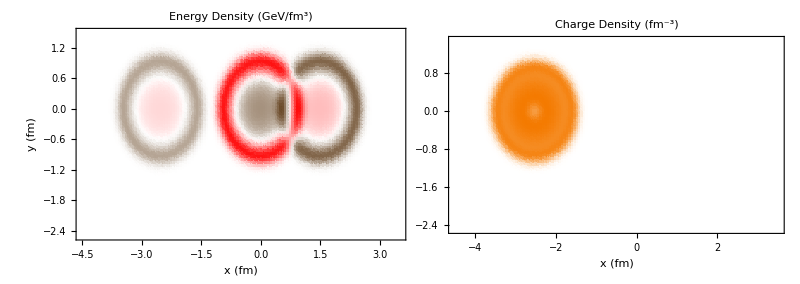

## Bottom Plot

```mathematica
Lambda0Data= Import["densities0_Hot.dat"][[2;;]];
```

```mathematica
EnergyDensity =Transpose[{Lambda0Data[[All,1]],Lambda0Data[[All,2]],Lambda0Data[[All,3]]-Commonest[Lambda0Data[[All,3]]][[1]]}];
ChargeDensity =Transpose[{Lambda0Data[[All,1]],Lambda0Data[[All,2]],Lambda0Data[[All,5]]}];
```

```mathematica
energydensity2color[z_]:=Blend[{White,RGBColor[0.6392156862745098,0.45098039215686275,0.3176470588235294],RGBColor[0.23137254901960785,0.1607843137254902,0.11372549019607843]},z];
```

```mathematica
energydensitycolor[z_]:=Blend[{{Min[EnergyDensity[[All,3]]],Red},{0,White},{Max[EnergyDensity[[All,3]]],Darker[Brown]}},z];
chargedensitycolor[z_]:=Blend[{{Min[ChargeDensity[[All,3]]],RGBColor[0.,0.5764705882352941,0.5764705882352941]},{0,White},{Max[ChargeDensity[[All,3]]],RGBColor[0.9568627450980393,0.47843137254901963,0.]}},z];
```

```mathematica
EnergyDensityPlot = ListDensityPlot[EnergyDensity,PlotRange->{{-3,4.5},{-2.5,1.5}},ColorFunction->(energydensitycolor[#]&),ColorFunctionScaling->False,Axes->False,LabelStyle->Directive[15,Bold,Black],Frame->True,FrameStyle->Directive[Black,Bold],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->300,LegendLayout->"Row",LabelStyle->Directive[Black,14]],Scaled[{0.47,0.15}]],ImageSize->450,AspectRatio->1/2,ImagePadding->{{All,0},{All,0}},PlotLabel->"Energy Density (GeV/fm^3)",FrameLabel->{{Style["y (fm)",Bold,20,Black],None},{Style["x (fm)",Bold,20,Black],None}},
FrameTicksStyle->
{{Directive[Black,20],
Directive[FontOpacity->0,FontSize->0]
},
{Directive[Black,20],
Directive[FontOpacity->0,FontSize->0]}}];
```

```mathematica
ChargeDensityPlot = ListDensityPlot[ChargeDensity,PlotRange->{{-3,4.5},{-2.5,1.5}},ColorFunction->(chargedensitycolor[#]&),ColorFunctionScaling->False,Axes->False,LabelStyle->Directive[15,Bold,Black],Frame->True,FrameStyle->Directive[Black,Bold],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->300,LegendLayout->"Row",LabelStyle->Directive[Black,14]],Scaled[{0.47,0.15}]],ImageSize->450,AspectRatio->1/2,ImagePadding->{{0,All},{All,0}},PlotLabel->"Charge Density (fm^-3)",FrameLabel->{{Style["",Bold,20,Black],None},{Style["x (fm)",Bold,20,Black],None}},
FrameTicksStyle->
{{Directive[FontOpacity->0,FontSize->0],
Directive[Black,20]
},
{Directive[Black,20],
Directive[FontOpacity->0,FontSize->0]}}];
```

```mathematica
GraphicsRow[{
EnergyDensityPlot,
ChargeDensityPlot
},ImageSize->800,Spacings->0]
```